```mathematica
inf["neuralNetExplorations`"]
```

```mathematica
?
```

```mathematica
hp=2;
```

```mathematica
net=NetChain[
{
LinearLayer[hp],
BatchNormalizationLayer[],
Ramp,
LinearLayer[hp],
BatchNormalizationLayer[],
Ramp,

LinearLayer[hp],
BatchNormalizationLayer[],
Ramp,

LinearLayer[1]
},"Input"->"Scalar","Output"->"Scalar"
]//NetInitialize;
```

```mathematica
weights[net]//Length
```

43

```mathematica
NetGraph[net]
```

NetGraph[<>]

```mathematica
plotData[points_,color_]:=ListPlot[points,PlotStyle->Directive[color,PointSize[.01]],FrameTicks->False,PlotRangePadding->0.1,PlotRange->All];
```

```mathematica
plot=plotData[List@@@datum,GrayLevel[0.7]];
plotSolution[net_,t_]:=Show[plot,plotData[Transpose[{Range[-20,30,.02],net@Range[-20,30,.02]}],Magenta],Epilog->Text[t,{10,0.9},{-1,0}]]
```

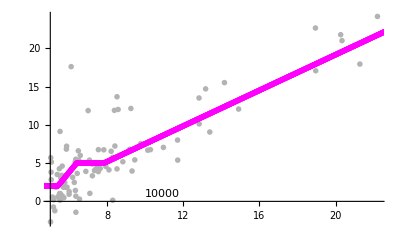

```mathematica
trained=NetTrain[net,Rule@@@datum,
Method->{"SGD","LearningRate"->0.001},
TargetDevice->"CPU",
MaxTrainingRounds->Quantity[20,"Seconds"],TrainingProgressReporting->{Style[Grid[{{plotSolution[#Net,#AbsoluteBatch]},{}}],ImageSizeMultipliers->{1, 1}]&,"Interval"->0.1}];
Style[Grid[{{plotSolution[trained,10000]}}],ImageSizeMultipliers->{1, 1}]
```